# Section 11.9

```mathematica
Series[Log[1+x],{x,0,10}]
```

x-x^2/2+x^3/3-x^4/4+x^5/5-x^6/6+x^7/7-x^8/8+x^9/9-x^10/10+O[x]^11

```mathematica
Series[ArcTan[x],{x,0,10}]
```

x-x^3/3+x^5/5-x^7/7+x^9/9+O[x]^11

```mathematica
SumConvergence[(-1)^n*x^(2n+1)/(2n+1),n]
```

Abs[x]<1

```mathematica
Series[Log[1+x^2],{x,0,10}]
```

x^2-x^4/2+x^6/3-x^8/4+x^10/5+O[x]^11

```mathematica
Integrate[2x/(1+x^2),x]
```

Log[1+x^2]

```mathematica
D[Log[(1+x^2)],x]
```

(2 x)/(1+x^2)

```mathematica
SumConvergence[(-1)^n*x^(2n+2)/(n+1),n]
```

Abs[x]<1

```mathematica
D[ArcTan[3x],x]
```

3/(1+9 x^2)

```mathematica
Series[ArcTan[3x],{x,0,10}]
```

3 x-9 x^3+(243 x^5)/5-(2187 x^7)/7+2187 x^9+O[x]^11

```mathematica
SumConvergence[(-1)^n*(3x)^(2n+1)/(2n+1),n]
```

Abs[x]<1/3

```mathematica
Integrate[t/(t^2+16),t]
```

1/2 Log[16+t^2]

```mathematica
Series[Integrate[ArcTan[x^8],x],{x,0,10}]
```

Series::ztest: Unable to decide whether numeric quantities {«11»+(4 ⅈ («1») ((4096 («1»)^6)/((Times[«1»]+«1»)^12 (1+«1»)^6)+(5120 «1»)/((«1»)^10 «1»)+(«1»)/(«1»)+64/((«1»)^6 («1»)^3)))/(7 (-(-1)^(1/16)-(-1)^(15/16)) (1-Plus[«2»]^2/Plus[«2»]^2)),«10»+(4 ⅈ «1» («1»))/(5 «1» (1-«1»))+(4 «3»)/(5 (-(«1»)^(1/«2»)-«1») (1-(«1»)^2/(«1»)^2))} are equal to zero. Assuming they are.

1/2 (2-1/(9 (1+Cot[π/16]^2))4 Cot[π/16] ((256 Cot[π/16]^8 Csc[π/16]^8)/((1+Cot[π/16]^2)^8)-(448 Cot[π/16]^6 Csc[π/16]^8)/((1+Cot[π/16]^2)^7)+(240 Cot[π/16]^4 Csc[π/16]^8)/((1+Cot[π/16]^2)^6)-(40 Cot[π/16]^2 Csc[π/16]^8)/((1+Cot[π/16]^2)^5)+Csc[π/16]^8/((1+Cot[π/16]^2)^4))+1/(9 (1+Cot[(3 π)/16]^2))4 Cot[(3 π)/16] ((256 Cot[(3 π)/16]^8 Csc[(3 π)/16]^8)/((1+Cot[(3 π)/16]^2)^8)-(448 Cot[(3 π)/16]^6 Csc[(3 π)/16]^8)/((1+Cot[(3 π)/16]^2)^7)+(240 Cot[(3 π)/16]^4 Csc[(3 π)/16]^8)/((1+Cot[(3 π)/16]^2)^6)-(40 Cot[(3 π)/16]^2 Csc[(3 π)/16]^8)/((1+Cot[(3 π)/16]^2)^5)+Csc[(3 π)/16]^8/((1+Cot[(3 π)/16]^2)^4))+4/9 (9 Cos[π/16]-120 Cos[π/16]^3+432 Cos[π/16]^5-576 Cos[π/16]^7+256 Cos[π/16]^9) Sin[π/16]-4/9 Cos[π/16] (9 Sin[π/16]-120 Sin[π/16]^3+432 Sin[π/16]^5-576 Sin[π/16]^7+256 Sin[π/16]^9)-4/9 (9 Cos[(3 π)/16]-120 Cos[(3 π)/16]^3+432 Cos[(3 π)/16]^5-576 Cos[(3 π)/16]^7+256 Cos[(3 π)/16]^9) Sin[(3 π)/16]+4/9 Cos[(3 π)/16] (9 Sin[(3 π)/16]-120 Sin[(3 π)/16]^3+432 Sin[(3 π)/16]^5-576 Sin[(3 π)/16]^7+256 Sin[(3 π)/16]^9)+1/(9 (1+Tan[π/16]^2))4 Tan[π/16] ((256 Sec[π/16]^8 Tan[π/16]^8)/((1+Tan[π/16]^2)^8)-(448 Sec[π/16]^8 Tan[π/16]^6)/((1+Tan[π/16]^2)^7)+(240 Sec[π/16]^8 Tan[π/16]^4)/((1+Tan[π/16]^2)^6)-(40 Sec[π/16]^8 Tan[π/16]^2)/((1+Tan[π/16]^2)^5)+Sec[π/16]^8/((1+Tan[π/16]^2)^4))-1/(9 (1+Tan[(3 π)/16]^2))4 Tan[(3 π)/16] ((256 Sec[(3 π)/16]^8 Tan[(3 π)/16]^8)/((1+Tan[(3 π)/16]^2)^8)-(448 Sec[(3 π)/16]^8 Tan[(3 π)/16]^6)/((1+Tan[(3 π)/16]^2)^7)+(240 Sec[(3 π)/16]^8 Tan[(3 π)/16]^4)/((1+Tan[(3 π)/16]^2)^6)-(40 Sec[(3 π)/16]^8 Tan[(3 π)/16]^2)/((1+Tan[(3 π)/16]^2)^5)+Sec[(3 π)/16]^8/((1+Tan[(3 π)/16]^2)^4))) x^9+O[x]^11

```mathematica
Sum[n*(n-1)*x^n,{n,2,Infinity}]
```

-(2 x^2)/(-1+x)^3

```mathematica
D[x^2/(1-x)^2,x]
```

(2 x)/(1-x)^2+(2 x^2)/(1-x)^3

```mathematica
Sum[n*(n-1)*x^n,{n,1,Infinity}]
```

-(2 x^2)/(-1+x)^3

```mathematica
Sum[n*x^n,{n,1,Infinity}]
```

x/(-1+x)^2

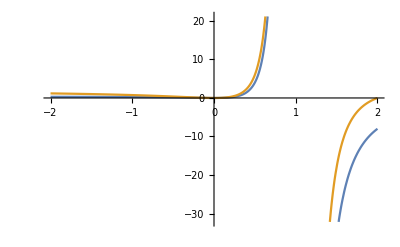

```mathematica
Plot[{-2x^2/(-1+x)^3,(4x^2-2x^3)/(1-x)^3},{x,-2,2}]
```